```mathematica
(*Import data from the specified file*)dataset=Import["/Users/humayrajeba/Documents/Wolfram Mathematica/THzBlock/Set3_H=135cm_L13=450cm_L12=300cm/DATA_UNCAL_Meas23"];
```

```mathematica
(*Define parameters for processing*)
avgParam=20;
percentage=5;
{time,signal}={dataset[[1;;,1]],dataset[[1;;,2]]};
```

```mathematica
signal
```

```mathematica
signal
```

```mathematica
signal
```

```mathematica
(*Calculate the weighted signal and its exponential moving average*)
weightedSignal=10*Log10[signal]
```

```mathematica
decayRate=0.005;
movingAvg=Re[ExponentialMovingAverage[weightedSignal,decayRate]]
```

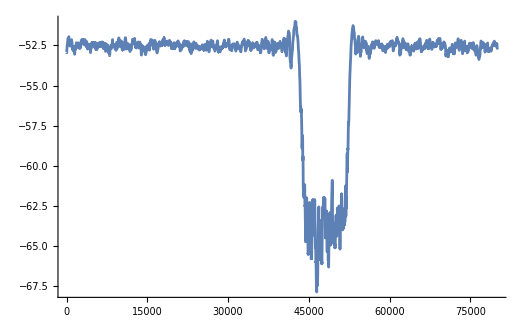

```mathematica
ListLinePlot[movingAvg,PlotRange->All]
```

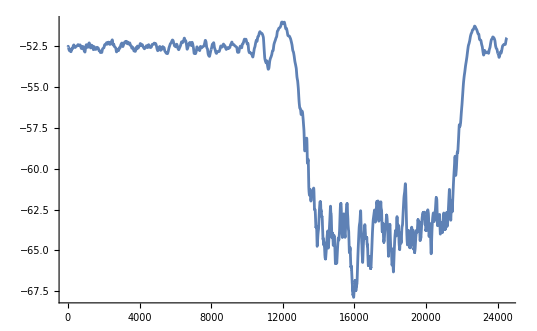

```mathematica
ListLinePlot@Take[movingAvg,{30500,55000}]
```

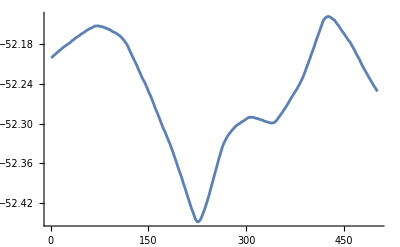

```mathematica
ListLinePlot@Take[movingAvg,{3000,3500}]
```

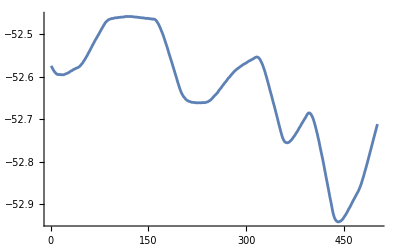

```mathematica
ListLinePlot@Take[movingAvg,{4000,4500}]
```

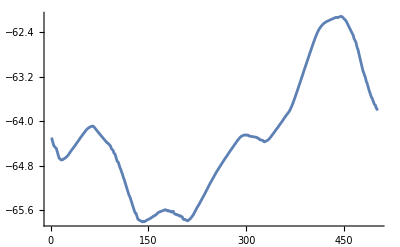

```mathematica
ListLinePlot@Take[movingAvg,{45300,45800}]
```

```mathematica
nonBlocked=Take[movingAvg,{3000,3500}];
oscillating=Take[movingAvg,{4000,4500}];
blocked=Take[movingAvg,{45300,45800}];
```

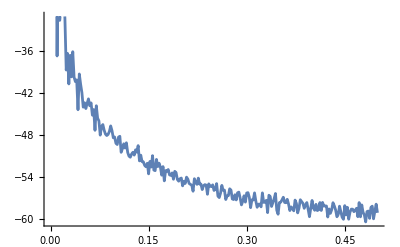

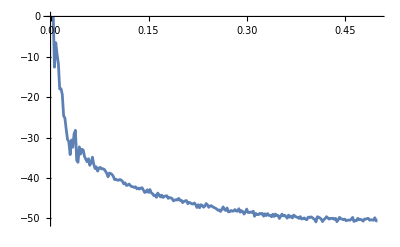

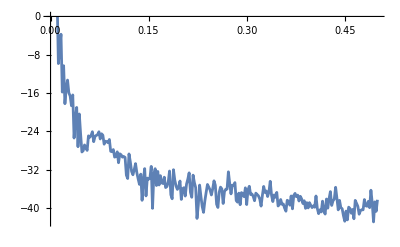

```mathematica
periodogramNonBlocked=Periodogram[nonBlocked,PlotStyle->DarkRed]
periodogramOscillating=Periodogram[oscillating,PlotStyle->DarkMagenta]
periodogramBlocked=Periodogram[blocked,PlotStyle->DarkGreen]
```

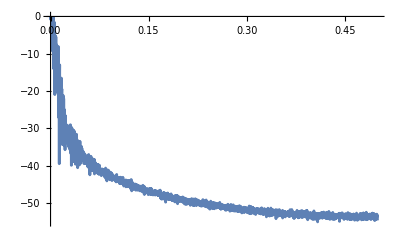

-Graphics-

```mathematica
powerSpectrumNonBlocked=PeriodogramArray[nonBlocked];
powerSpectrumOscillating=PeriodogramArray[oscillating];
powerSpectrumBlocked=PeriodogramArray[blocked];
```

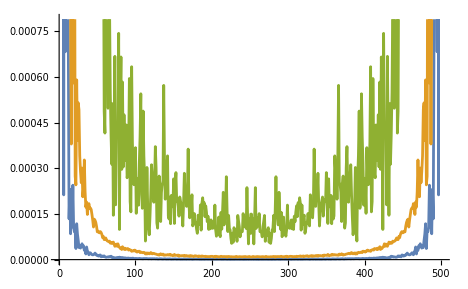

```mathematica
ListLinePlot[{powerSpectrumNonBlocked,powerSpectrumOscillating,powerSpectrumBlocked}]
```

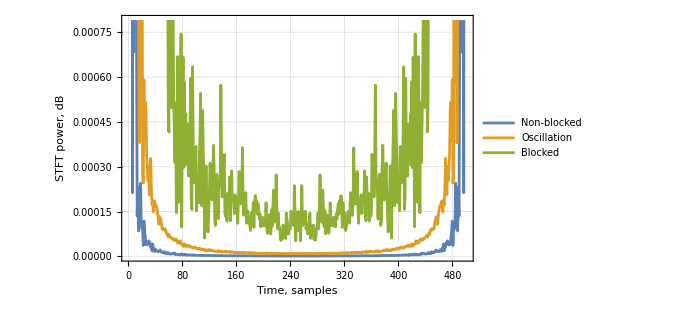

```mathematica
ListLinePlot[{powerSpectrumNonBlocked,powerSpectrumOscillating,powerSpectrumBlocked},GridLines->Automatic,LabelStyle->{FontSize->13,FontFamily->"Times New Roman"},Frame->True,FrameLabel->{Style["Time, samples",Black,15],Style["STFT power, dB",Black,15]},PlotLegends->Placed[LineLegend[{"Non-blocked","Oscillation","Blocked"},LegendFunction->(Framed[#,FrameMargins->0,Background->White,FrameStyle->Lighter[Gray]]&),LabelStyle->Directive[FontSize->13],LegendMargins->5,Spacings->0.35],{0.5,0.7}],ImageSize->500]
```

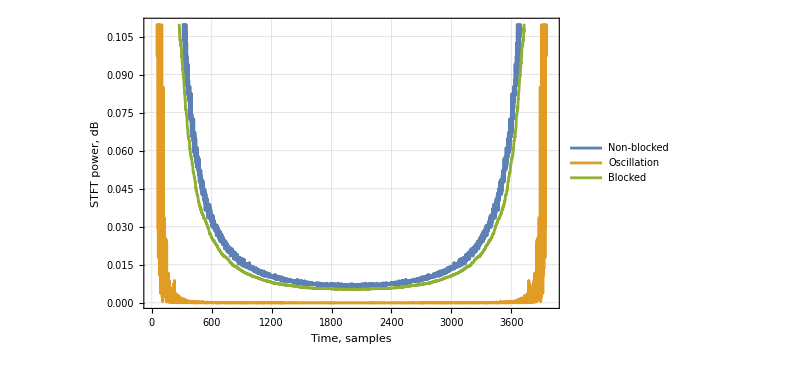

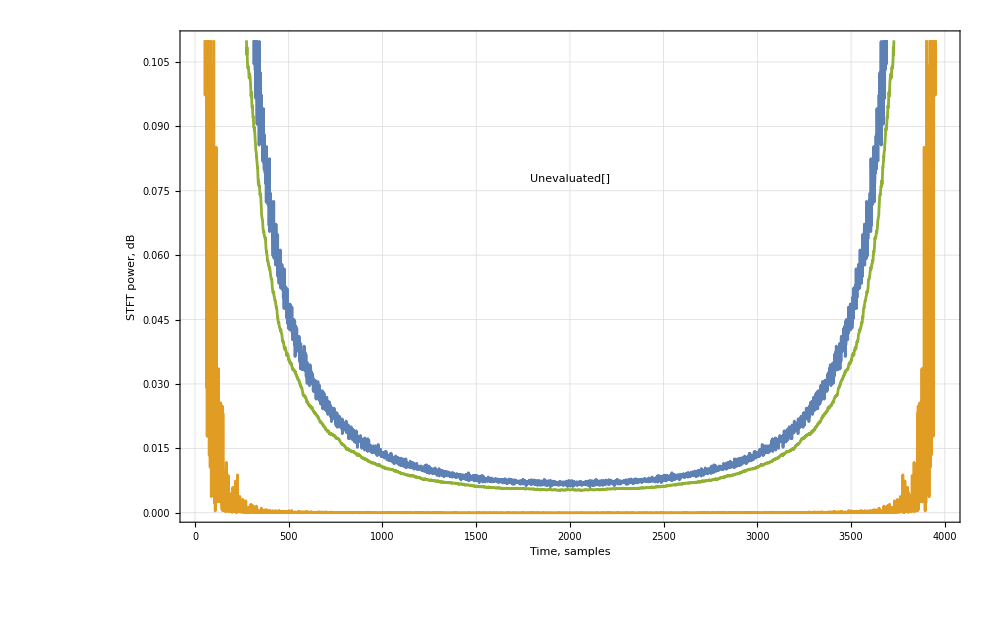

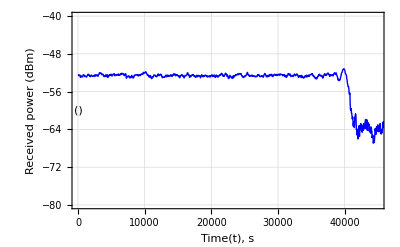

```mathematica
ListLinePlot[movingAvg,FillingStyle->Directive[Opacity[0.1],LightBlue],PlotStyle->{Thick,Blue},BaseStyle->{FontFamily->"Times",FontColor->RGBColor[0.01,0.01,0.01],FontSize->13},FrameLabel->{"Time(t), s","Received power (dBm)"},PlotTheme->"Detailed",Joined->True,PlotRange->{{0,45000},{-80,-40}},Epilog->{Text[Column[{Style["",FontSize->13,FontColor->RGBColor[0.01,0.01,0.01]],Style["()",FontSize->13,FontColor->RGBColor[0.01,0.01,0.01]]}],{-0.6,-60}],Text[Column[{Style["",FontSize->13,FontColor->RGBColor[0.01,0.01,0.01]],Style["",FontSize->13,FontColor->RGBColor[0.01,0.01,0.01]]}],{-0.15,-55}],Text[Column[{Style["",FontSize->10,FontColor->RGBColor[0.01,0.01,0.01]],Style["",FontSize->13,FontColor->RGBColor[0.01,0.01,0.01]]}],{0.1,-50}]}]
```

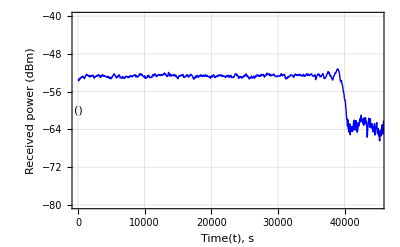

-Graphics-

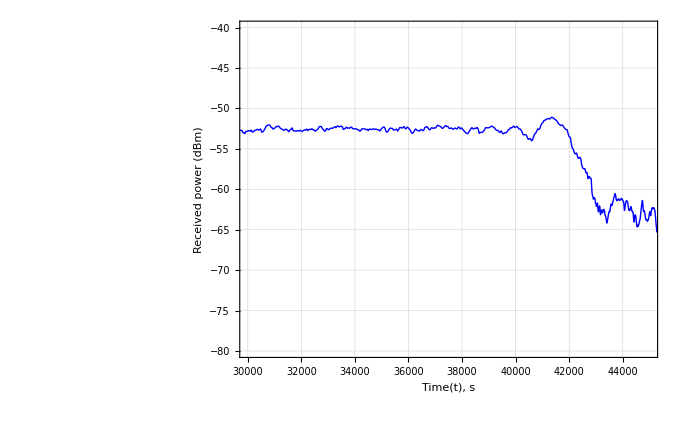

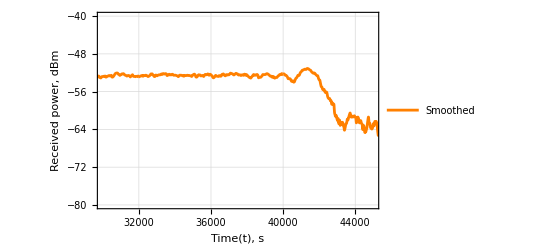

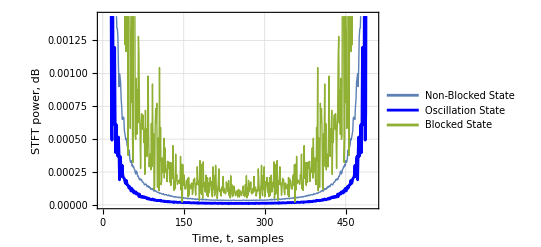

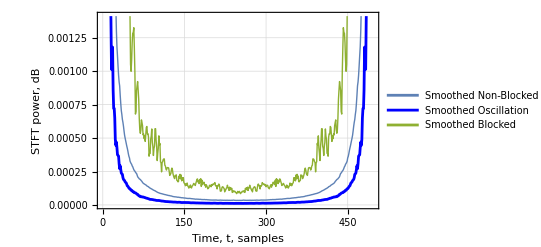

```mathematica
(*Define parameters for processing*)
avgParam=20;
percentage=5;
{time,signal}={dataset[[1;;,1]],dataset[[1;;,2]]};

(*Calculate the weighted signal and its exponential moving average*)
weightedSignal=10*Log10[signal];
decayRate=0.005;
movingAvg=Re[ExponentialMovingAverage[weightedSignal,decayRate]];

(*Plot the moving average of the signal with new colors*)
ListLinePlot[movingAvg,FillingStyle->Directive[Opacity[0.1],LightBlue],PlotStyle->{Thick,Blue},BaseStyle->{FontFamily->"Times",FontColor->RGBColor[0.01,0.01,0.01],FontSize->13},FrameLabel->{"Time(t), s","Received power (dBm)"},PlotTheme->"Detailed",Joined->True,PlotRange->{{30000,45000},{-80,-40}},Epilog->{Text[Column[{Style["Typical signal dynamics",FontSize->13,FontColor->RGBColor[0.01,0.01,0.01]],Style["(Non-blocked period)",FontSize->13,FontColor->RGBColor[0.01,0.01,0.01]]}],{-0.6,-60}],Text[Column[{Style["Oscillation",FontSize->13,FontColor->RGBColor[0.01,0.01,0.01]],Style["period",FontSize->13,FontColor->RGBColor[0.01,0.01,0.01]]}],{-0.15,-55}],Text[Column[{Style["Blocked",FontSize->10,FontColor->RGBColor[0.01,0.01,0.01]],Style["period",FontSize->13,FontColor->RGBColor[0.01,0.01,0.01]]}],{0.1,-50}]}]

(*Plot the smoothed version of the moving average*)
ListLinePlot[MovingAverage[movingAvg,5],FillingStyle->Directive[Opacity[0.1],LightBlue],PlotStyle->{Thick,Orange},BaseStyle->{FontFamily->"Times",FontColor->RGBColor[0.01,0.01,0.01],FontSize->13},FrameLabel->{"Time(t), s","Received power, dBm"},PlotTheme->"Detailed",Joined->True,PlotRange->{{30000,45000},{-80,-40}},PlotLegends->Placed[{"Smoothed"},After]]

(*Extract signal samples for different states*)
nonBlocked=Downsample[Take[movingAvg,{500,1000}],1];
oscillating=Downsample[Take[movingAvg,{2000,2500}],1];
blocked=Downsample[Take[movingAvg,{45300,45800}],1];

(*Compute periodograms for each state*)
periodogramNonBlocked=Periodogram[nonBlocked,PlotStyle->DarkRed];
periodogramOscillating=Periodogram[oscillating,PlotStyle->DarkMagenta];
periodogramBlocked=Periodogram[blocked,PlotStyle->DarkGreen];

(*Compute the power spectral density for each state*)
powerSpectrumNonBlocked=PeriodogramArray[nonBlocked];
powerSpectrumOscillating=PeriodogramArray[oscillating];
powerSpectrumBlocked=PeriodogramArray[blocked];

(*Plot the power spectral density for each state with new colors*)
ListLinePlot[{powerSpectrumNonBlocked,powerSpectrumOscillating,powerSpectrumBlocked},FillingStyle->Directive[Opacity[0.1],LightBlue],PlotLegends->Placed[LineLegend[{"Non-Blocked State","Oscillation State","Blocked State"},LabelStyle->{FontFamily->"Times New Roman",FontColor->RGBColor[0.01,0.01,0.01],FontSize->10},LegendMarkerSize->10,LegendLayout->"Column",Spacings->0.1,LegendMargins->0.1,LegendFunction->(Panel[#,Background->None,FrameMargins->None]&)],After],PlotStyle->{Thick,Blue,Thick,Orange,Thick,Green},BaseStyle->{FontFamily->"Times",FontColor->RGBColor[0.01,0.01,0.01],FontSize->13},FrameLabel->{"Time, t, samples","STFT power, dB"},PlotTheme->"Detailed",Joined->True]

(*Plot the smoothed version of the power spectral density*)
ListLinePlot[{MovingAverage[powerSpectrumNonBlocked,5],MovingAverage[powerSpectrumOscillating,5],MovingAverage[powerSpectrumBlocked,5]},FillingStyle->Directive[Opacity[0.1],LightBlue],PlotLegends->Placed[LineLegend[{"Smoothed Non-Blocked","Smoothed Oscillation","Smoothed Blocked"},LabelStyle->{FontFamily->"Times New Roman",FontColor->RGBColor[0.01,0.01,0.01],FontSize->10},LegendMarkerSize->10,LegendLayout->"Column",Spacings->0.1,LegendMargins->0.1,LegendFunction->(Panel[#,Background->None,FrameMargins->None]&)],After],PlotStyle->{Thick,Blue,Thick,Orange,Thick,Green},BaseStyle->{FontFamily->"Times",FontColor->RGBColor[0.01,0.01,0.01],FontSize->13},FrameLabel->{"Time, t, samples","STFT power, dB"},PlotTheme->"Detailed",Joined->True]
```

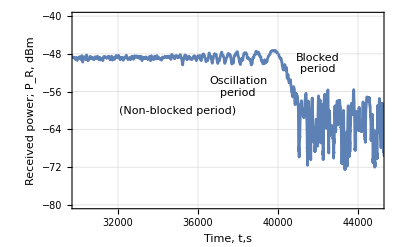
## 

NonBlocked Power: 0.122689

Oscillation Power: 0.44259

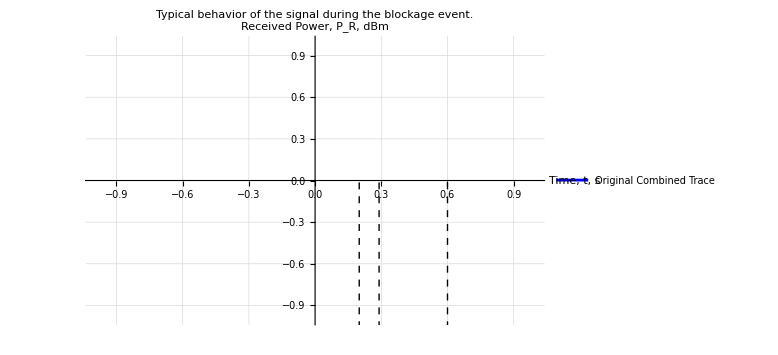
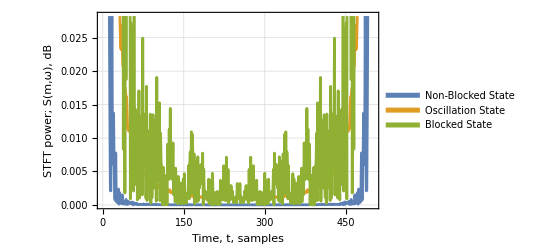

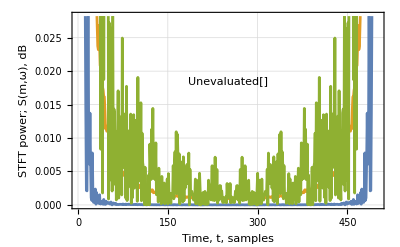
-Graphics-
-Graphics-

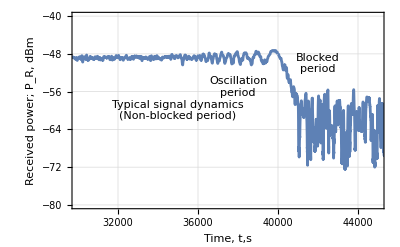

```mathematica
Show[%1222,Axes->True,AxesStyle->Gray]
```

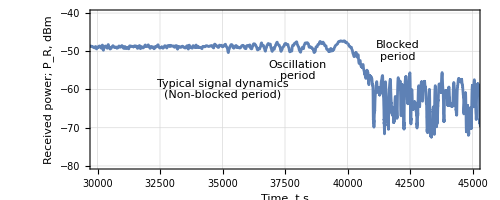

```mathematica
Show[%1239,AspectRatio->Automatic]
```

```mathematica
Show[%1240,AspectRatio->Full]
```

-Graphics-

```mathematica
Show[%1241,PlotLabel->None,LabelStyle->{GrayLevel[0],Italic,Bold}]
```

-Graphics-

-Graphics-

```mathematica
ClearAll
```

ClearAll

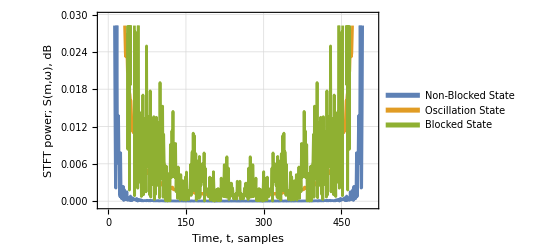

NonBlocked Power: 0.122689

Oscillation Power: 0.44259

Blockage Detected at Samples: {501,521,541,561,581,601,621,641,661,681,701,721,741,761,781,801,821,841,861,881,901,921,941,961,981,1001,1021,1041,1061,1081,1101,1121,1141,1161,1181,1201,1221,1241,1261,1281,1301,1321,1341,1361,1381,1401,1421,1441,1461,1481,1501,1521,1541,1561,1581,1601,1621,1641,1661,1681,1701,1721,1741,1761,1781,1801,1821,1841,1861,1881,1901,1921,1941,1961,1981,2001,2021,2041,2061,2081,2101,2121,2141,2161,2181,2201,2221,2241,2261,2281,2301,2321,2341,2361,2381,2401,2421,2441,2461,2481,2501,2521,2541,2561,2581,2601,2621,2641,2661,2681,2701,2721,2741,2761,2781,2801,2821,2841,2861,2881,2901,2921,2941,2961,2981,3001,3021,3041,3061,3081,3101,3121,3141,3161,3181,3201,3221,3241,3261,3281,3301,3321,3341,3361,3381,3401,3421,3441,3461,3481,3501,3521,3541,3561,3581,3601,3621,3641,3661,3681,3701,3721,3741,3761,3781,3801,3821,3841,3861,3881,3901,3921,3941,3961,3981,4001,4021,4041,4061,4081,4101,4121,4141,4161,4181,4201,4221,4241,4261,4281,4301,4321,4341,4361,4381,4401,4421,4441,4461,4481,4501,4521,4541,4561,4581,4601,4621,4641,4661,4681,4701,4721,4741,4761,4781,4801,4821,4841,4861,4881,4901,4921,4941,4961,4981,5001,5021,5041,5061,5081,5101,5121,5141,5161,5181,5201,5221,5241,5261,5281,5301,5321,5341,5361,5381,5401,5421,5441,5461,5481,5501,5521,5541,5561,5581,5601,5621,5641,5661,5681,5701,5721,5741,5761,5781,5801,5821,5841,5861,5881,5901,5921,5941,5961,5981,6001,6021,6041,6061,6081,6101,6121,6141,6161,6181,6201,6221,6241,6261,6281,6301,6321,6341,6361,6381,6401,6421,6441,6461,6481,6501,6521,6541,6561,6581,6601,6621,6641,6661,6681,6701,6721,6741,6761,6781,6801,6821,6841,6861,6881,6901,6921,6941,6961,6981,7001,7021,7041,7061,7081,7101,7121,7141,7161,7181,7201,7221,7241,7261,7281,7301,7321,7341,7361,7381,7401,7421,7441,7461,7481,7501,7521,7541,7561,7581,7601,7621,7641,7661,7681,7701,7721,7741,7761,7781,7801,7821,7841,7861,7881,7901,7921,7941,7961,7981,8001,8021,8041,8061,8081,8101,8121,8141,8161,8181,8201,8221,8241,8261,8281,8301,8321,8341,8361,8381,8401,8421,8441,8461,8481,8501,8521,8541,8561,8581,8601,8621,8641,8661,8681,8701,8721,8741,8761,8781,8801,8821,8841,8861,8881,8901,8921,8941,8961,8981,9001,9021,9041,9061,9081,9101,9121,9141,9161,9181,9201,9221,9241,9261,9281,9301,9321,9341,9361,9381,9401,9421,9441,9461,9481,9501,9521,9541,9561,9581,9601,9621,9641,9661,9681,9701,9721,9741,9761,9781,9801,9821,9841,9861,9881,9901,9921,9941,9961,9981,10001,10021,10041,10061,10081,10101,10121,10141,10161,10181,10201,10221,10241,10261,10281,10301,10321,10341,10361,10381,10401,10421,10441,10461,10481,10501,10521,10541,10561,10581,10601,10621,10641,10661,10681,10701,10721,10741,10761,10781,10801,10821,10841,10861,10881,10901,10921,10941,10961,10981,11001,11021,11041,11061,11081,11101,11121,11141,11161,11181,11201,11221,11241,11261,11281,11301,11321,11341,11361,11381,11401,11421,11441,11461,11481,11501,11521,11541,11561,11581,11601,11621,11641,11661,11681,11701,11721,11741,11761,11781,11801,11821,11841,11861,11881,11901,11921,11941,11961,11981,12001,12021,12041,12061,12081,12101,12121,12141,12161,12181,12201,12221,12241,12261,12281,12301,12321,12341,12361,12381,12401,12421,12441,12461,12481,12501,12521,12541,12561,12581,12601,12621,12641,12661,12681,12701,12721,12741,12761,12781,12801,12821,12841,12861,12881,12901,12921,12941,12961,12981,13001,13021,13041,13061,13081,13101,13121,13141,13161,13181,13201,13221,13241,13261,13281,13301,13321,13341,13361,13381,13401,13421,13441,13461,13481,13501,13521,13541,13561,13581,13601,13621,13641,13661,13681,13701,13721,13741,13761,13781,13801,13821,13841,13861,13881,13901,13921,13941,13961,13981,14001,14021,14041,14061,14081,14101,14121,14141,14161,14181,14201,14221,14241,14261,14281,14301,14321,14341,14361,14381,14401,14421,14441,14461,14481,14501,14521,14541,14561,14581,14601,14621,14641,14661,14681,14701,14721,14741,14761,14781,14801,14821,14841,14861,14881,14901,14921,14941,14961,14981,15001,15021,15041,15061,15081,15101,15121,15141,15161,15181,15201,15221,15241,15261,15281,15301,15321,15341,15361,15381,15401,15421,15441,15461,15481,15501,15521,15541,15561,15581,15601,15621,15641,15661,15681,15701,15721,15741,15761,15781,15801,15821,15841,15861,15881,15901,15921,15941,15961,15981,16001,16021,16041,16061,16081,16101,16121,16141,16161,16181,16201,16221,16241,16261,16281,16301,16321,16341,16361,16381,16401,16421,16441,16461,16481,16501,16521,16541,16561,16581,16601,16621,16641,16661,16681,16701,16721,16741,16761,16781,16801,16821,16841,16861,16881,16901,16921,16941,16961,16981,17001,17021,17041,17061,17081,17101,17121,17141,17161,17181,17201,17221,17241,17261,17281,17301,17321,17341,17361,17381,17401,17421,17441,17461,17481,17501,17521,17541,17561,17581,17601,17621,17641,17661,17681,17701,17721,17741,17761,17781,17801,17821,17841,17861,17881,17901,17921,17941,17961,17981,18001,18021,18041,18061,18081,18101,18121,18141,18161,18181,18201,18221,18241,18261,18281,18301,18321,18341,18361,18381,18401,18421,18441,18461,18481,18501,18521,18541,18561,18581,18601,18621,18641,18661,18681,18701,18721,18741,18761,18781,18801,18821,18841,18861,18881,18901,18921,18941,18961,18981,19001,19021,19041,19061,19081,19101,19121,19141,19161,19181,19201,19221,19241,19261,19281,19301,19321,19341,19361,19381,19401,19421,19441,19461,19481,19501,19521,19541,19561,19581,19601,19621,19641,19661,19681,19701,19721,19741,19761,19781,19801,19821,19841,19861,19881,19901,19921,19941,19961,19981,20001,20021,20041,20061,20081,20101,20121,20141,20161,20181,20201,20221,20241,20261,20281,20301,20321,20341,20361,20381,20401,20421,20441,20461,20481,20501,20521,20541,20561,20581,20601,20621,20641,20661,20681,20701,20721,20741,20761,20781,20801,20821,20841,20861,20881,20901,20921,20941,20961,20981,21001,21021,21041,21061,21081,21101,21121,21141,21161,21181,21201,21221,21241,21261,21281,21301,21321,21341,21361,21381,21401,21421,21441,21461,21481,21501,21521,21541,21561,21581,21601,21621,21641,21661,21681,21701,21721,21741,21761,21781,21801,21821,21841,21861,21881,21901,21921,21941,21961,21981,22001,22021,22041,22061,22081,22101,22121,22141,22161,22181,22201,22221,22241,22261,22281,22301,22321,22341,22361,22381,22401,22421,22441,22461,22481,22501,22521,22541,22561,22581,22601,22621,22641,22661,22681,22701,22721,22741,22761,22781,22801,22821,22841,22861,22881,22901,22921,22941,22961,22981,23001,23021,23041,23061,23081,23101,23121,23141,23161,23181,23201,23221,23241,23261,23281,23301,23321,23341,23361,23381,23401,23421,23441,23461,23481,23501,23521,23541,23561,23581,23601,23621,23641,23661,23681,23701,23721,23741,23761,23781,23801,23821,23841,23861,23881,23901,23921,23941,23961,23981,24001,24021,24041,24061,24081,24101,24121,24141,24161,24181,24201,24221,24241,24261,24281,24301,24321,24341,24361,24381,24401,24421,24441,24461,24481,24501,24521,24541,24561,24581,24601,24621,24641,24661,24681,24701,24721,24741,24761,24781,24801,24821,24841,24861,24881,24901,24921,24941,24961,24981,25001,25021,25041,25061,25081,25101,25121,25141,25161,25181,25201,25221,25241,25261,25281,25301,25321,25341,25361,25381,25401,25421,25441,25461,25481,25501,25521,25541,25561,25581,25601,25621,25641,25661,25681,25701,25721,25741,25761,25781,25801,25821,25841,25861,25881,25901,25921,25941,25961,25981,26001,26021,26041,26061,26081,26101,26121,26141,26161,26181,26201,26221,26241,26261,26281,26301,26321,26341,26361,26381,26401,26421,26441,26461,26481,26501,26521,26541,26561,26581,26601,26621,26641,26661,26681,26701,26721,26741,26761,26781,26801,26821,26841,26861,26881,26901,26921,26941,26961,26981,27001,27021,27041,27061,27081,27101,27121,27141,27161,27181,27201,27221,27241,27261,27281,27301,27321,27341,27361,27381,27401,27421,27441,27461,27481,27501,27521,27541,27561,27581,27601,27621,27641,27661,27681,27701,27721,27741,27761,27781,27801,27821,27841,27861,27881,27901,27921,27941,27961,27981,28001,28021,28041,28061,28081,28101,28121,28141,28161,28181,28201,28221,28241,28261,28281,28301,28321,28341,28361,28381,28401,28421,28441,28461,28481,28501,28521,28541,28561,28581,28601,28621,28641,28661,28681,28701,28721,28741,28761,28781,28801,28821,28841,28861,28881,28901,28921,28941,28961,28981,29001,29021,29041,29061,29081,29101,29121,29141,29161,29181,29201,29221,29241,29261,29281,29301,29321,29341,29361,29381,29401,29421,29441,29461,29481,29501,29521,29541,29561,29581,29601,29621,29641,29661,29681,29701,29721,29741,29761,29781,29801,29821,29841,29861,29881,29901,29921,29941,29961,29981,30001,30021,30041,30061,30081,30101,30121,30141,30161,30181,30201,30221,30241,30261,30281,30301,30321,30341,30361,30381,30401,30421,30441,30461,30481,30501,30521,30541,30561,30581,30601,30621,30641,30661,30681,30701,30721,30741,30761,30781,30801,30821,30841,30861,30881,30901,30921,30941,30961,30981,31001,31021,31041,31061,31081,31101,31121,31141,31161,31181,31201,31221,31241,31261,31281,31301,31321,31341,31361,31381,31401,31421,31441,31461,31481,31501,31521,31541,31561,31581,31601,31621,31641,31661,31681,31701,31721,31741,31761,31781,31801,31821,31841,31861,31881,31901,31921,31941,31961,31981,32001,32021,32041,32061,32081,32101,32121,32141,32161,32181,32201,32221,32241,32261,32281,32301,32321,32341,32361,32381,32401,32421,32441,32461,32481,32501,32521,32541,32561,32581,32601,32621,32641,32661,32681,32701,32721,32741,32761,32781,32801,32821,32841,32861,32881,32901,32921,32941,32961,32981,33001,33021,33041,33061,33081,33101,33121,33141,33161,33181,33201,33221,33241,33261,33281,33301,33321,33341,33361,33381,33401,33421,33441,33461,33481,33501,33521,33541,33561,33581,33601,33621,33641,33661,33681,33701,33721,33741,33761,33781,33801,33821,33841,33861,33881,33901,33921,33941,33961,33981,34001,34021,34041,34061,34081,34101,34121,34141,34161,34181,34201,34221,34241,34261,34281,34301,34321,34341,34361,34381,34401,34421,34441,34461,34481,34501,34521,34541,34561,34581,34601,34621,34641,34661,34681,34701,34721,34741,34761,34781,34801,34821,34841,34861,34881,34901,34921,34941,34961,34981,35001,35021,35041,35061,35081,35101,35121,35141,35161,35181,35201,35221,35241,35261,35281,35301,35321,35341,35361,35381,35401,35421,35441,35461,35481,35501,35521,35541,35561,35581,35601,35621,35641,35661,35681,35701,35721,35741,35761,35781,35801,35821,35841,35861,35881,35901,35921,35941,35961,35981,36001,36021,36041,36061,36081,36101,36121,36141,36161,36181,36201,36221,36241,36261,36281,36301,36321,36341,36361,36381,36401,36421,36441,36461,36481,36501,36521,36541,36561,36581,36601,36621,36641,36661,36681,36701,36721,36741,36761,36781,36801,36821,36841,36861,36881,36901,36921,36941,36961,36981,37001,37021,37041,37061,37081,37101,37121,37141,37161,37181,37201,37221,37241,37261,37281,37301,37321,37341,37361,37381,37401,37421,37441,37461,37481,37501,37521,37541,37561,37581,37601,37621,37641,37661,37681,37701,37721,37741,37761,37781,37801,37821,37841,37861,37881,37901,37921,37941,37961,37981,38001,38021,38041,38061,38081,38101,38121,38141,38161,38181,38201,38221,38241,38261,38281,38301,38321,38341,38361,38381,38401,38421,38441,38461,38481,38501,38521,38541,38561,38581,38601,38621,38641,38661,38681,38701,38721,38741,38761,38781,38801,38821,38841,38861,38881,38901,38921,38941,38961,38981,39001,39021,39041,39061,39081,39101,39121,39141,39161,39181,39201,39221,39241,39261,39281,39301,39321,39341,39361,39381,39401,39421,39441,39461,39481,39501,39521,39541,39561,39581,39601,39621,39641,39661,39681,39701,39721,39741,39761,39781,39801,39821,39841,39861,39881,39901,39921,39941,39961,39981,40001,40021,40041,40061,40081,40101,40121,40141,40161,40181,40201,40221,40241,40261,40281,40301,40321,40341,40361,40381,40401,40421,40441,40461,40481,40501,40521,40541,40561,40581,40601,40621,40641,40661,40681,40701,40721,40741,40761,40781,40801,40821,40841,40861,40881,40901,40921,40941,40961,40981,41001,41021,41041,41061,41081,41101,41121,41141,41161,41181,41201,41221,41241,41261,41281,41301,41321,41341,41361,41381,41401,41421,41441,41461,41481,41501,41521,41541,41561,41581,41601,41621,41641,41661,41681,41701,41721,41741,41761,41781,41801,41821,41841,41861,41881,41901,41921,41941,41961,41981,42001,42021,42041,42061,42081,42101,42121,42141,42161,42181,42201,42221,42241,42261,42281,42301,42321,42341,42361,42381,42401,42421,42441,42461,42481,42501,42521,42541,42561,42581,42601,42621,42641,42661,42681,42701,42721,42741,42761,42781,42801,42821,42841,42861,42881,42901,42921,42941,42961,42981,43001,43021,43041,43061,43081,43101,43121,43141,43161,43181,43201,43221,43241,43261,43281,43301,43321,43341,43361,43381,43401,43421,43441,43461,43481,43501,43521,43541,43561,43581,43601,43621,43641,43661,43681,43701,43721,43741,43761,43781,43801,43821,43841,43861,43881,43901,43921,43941,43961,43981,44001,44021,44041,44061,44081,44101,44121,44141,44161,44181,44201,44221,44241,44261,44281,44301,44321,44341,44361,44381,44401,44421,44441,44461,44481,44501,44521,44541,44561,44581,44601,44621,44641,44661,44681,44701,44721,44741,44761,44781,44801,44821,44841,44861,44881,44901,44921,44941,44961,44981,45001,45021,45041,45061,45081,45101,45121,45141,45161,45181,45201,45221,45241,45261,45281,45301,45321,45341,45361,45381,45401,45421,45441,45461,45481,45501,45521,45541,45561,45581,45601,45621,45641,45661,45681,45701,45721,45741,45761,45781,45801,45821,45841,45861,45881,45901,45921,45941,45961,45981,46001,46021,46041,46061,46081,46101,46121,46141,46161,46181,46201,46221,46241,46261,46281,46301,46321,46341,46361,46381,46401,46421,46441,46461,46481,46501,46521,46541,46561,46581,46601,46621,46641,46661,46681,46701,46721,46741,46761,46781,46801,46821,46841,46861,46881,46901,46921,46941,46961,46981,47001,47021,47041,47061,47081,47101,47121,47141,47161,47181,47201,47221,47241,47261,47281,47301,47321,47341,47361,47381,47401,47421,47441,47461,47481,47501,47521,47541,47561,47581,47601,47621,47641,47661,47681,47701,47721,47741,47761,47781,47801,47821,47841,47861,47881,47901,47921,47941,47961,47981,48001,48021,48041,48061,48081,48101,48121,48141,48161,48181,48201,48221,48241,48261,48281,48301,48321,48341,48361,48381,48401,48421,48441,48461,48481,48501,48521,48541,48561,48581,48601,48621,48641,48661,48681,48701,48721,48741,48761,48781,48801,48821,48841,48861,48881,48901,48921,48941,48961,48981,49001,49021,49041,49061,49081,49101,49121,49141,49161,49181,49201,49221,49241,49261,49281,49301,49321,49341,49361,49381,49401,49421,49441,49461,49481,49501,49521,49541,49561,49581,49601,49621,49641,49661,49681,49701,49721,49741,49761,49781,49801,49821,49841,49861,49881,49901,49921,49941,49961,49981,50001,50021,50041,50061,50081,50101,50121,50141,50161,50181,50201,50221,50241,50261,50281,50301,50321,50341,50361,50381,50401,50421,50441,50461,50481,50501,50521,50541,50561,50581,50601,50621,50641,50661,50681,50701,50721,50741,50761,50781,50801,50821,50841,50861,50881,50901,50921,50941,50961,50981,51001,51021,51041,51061,51081,51101,51121,51141,51161,51181,51201,51221,51241,51261,51281,51301,51321,51341,51361,51381,51401,51421,51441,51461,51481,51501,51521,51541,51561,51581,51601,51621,51641,51661,51681,51701,51721,51741,51761,51781,51801,51821,51841,51861,51881,51901,51921,51941,51961,51981,52001,52021,52041,52061,52081,52101,52121,52141,52161,52181,52201,52221,52241,52261,52281,52301,52321,52341,52361,52381,52401,52421,52441,52461,52481,52501,52521,52541,52561,52581,52601,52621,52641,52661,52681,52701,52721,52741,52761,52781,52801,52821,52841,52861,52881,52901,52921,52941,52961,52981,53001,53021,53041,53061,53081,53101,53121,53141,53161,53181,53201,53221,53241,53261,53281,53301,53321,53341,53361,53381,53401,53421,53441,53461,53481,53501,53521,53541,53561,53581,53601,53621,53641,53661,53681,53701,53721,53741,53761,53781,53801,53821,53841,53861,53881,53901,53921,53941,53961,53981,54001,54021,54041,54061,54081,54101,54121,54141,54161,54181,54201,54221,54241,54261,54281,54301,54321,54341,54361,54381,54401,54421,54441,54461,54481,54501,54521,54541,54561,54581,54601,54621,54641,54661,54681,54701,54721,54741,54761,54781,54801,54821,54841,54861,54881,54901,54921,54941,54961,54981,55001,55021,55041,55061,55081,55101,55121,55141,55161,55181,55201,55221,55241,55261,55281,55301,55321,55341,55361,55381,55401,55421,55441,55461,55481,55501,55521,55541,55561,55581,55601,55621,55641,55661,55681,55701,55721,55741,55761,55781,55801,55821,55841,55861,55881,55901,55921,55941,55961,55981,56001,56021,56041,56061,56081,56101,56121,56141,56161,56181,56201,56221,56241,56261,56281,56301,56321,56341,56361,56381,56401,56421,56441,56461,56481,56501,56521,56541,56561,56581,56601,56621,56641,56661,56681,56701,56721,56741,56761,56781,56801,56821,56841,56861,56881,56901,56921,56941,56961,56981,57001,57021,57041,57061,57081,57101,57121,57141,57161,57181,57201,57221,57241,57261,57281,57301,57321,57341,57361,57381,57401,57421,57441,57461,57481,57501,57521,57541,57561,57581,57601,57621,57641,57661,57681,57701,57721,57741,57761,57781,57801,57821,57841,57861,57881,57901,57921,57941,57961,57981,58001,58021,58041,58061,58081,58101,58121,58141,58161,58181,58201,58221,58241,58261,58281,58301,58321,58341,58361,58381,58401,58421,58441,58461,58481,58501,58521,58541,58561,58581,58601,58621,58641,58661,58681,58701,58721,58741,58761,58781,58801,58821,58841,58861,58881,58901,58921,58941,58961,58981,59001,59021,59041,59061,59081,59101,59121,59141,59161,59181,59201,59221,59241,59261,59281,59301,59321,59341,59361,59381,59401,59421,59441,59461,59481,59501,59521,59541,59561,59581,59601,59621,59641,59661,59681,59701,59721,59741,59761,59781,59801,59821,59841,59861,59881,59901,59921,59941,59961,59981,60001,60021,60041,60061,60081,60101,60121,60141,60161,60181,60201,60221,60241,60261,60281,60301,60321,60341,60361,60381,60401,60421,60441,60461,60481,60501,60521,60541,60561,60581,60601,60621,60641,60661,60681,60701,60721,60741,60761,60781,60801,60821,60841,60861,60881,60901,60921,60941,60961,60981,61001,61021,61041,61061,61081,61101,61121,61141,61161,61181,61201,61221,61241,61261,61281,61301,61321,61341,61361,61381,61401,61421,61441,61461,61481,61501,61521,61541,61561,61581,61601,61621,61641,61661,61681,61701,61721,61741,61761,61781,61801,61821,61841,61861,61881,61901,61921,61941,61961,61981,62001,62021,62041,62061,62081,62101,62121,62141,62161,62181,62201,62221,62241,62261,62281,62301,62321,62341,62361,62381,62401,62421,62441,62461,62481,62501,62521,62541,62561,62581,62601,62621,62641,62661,62681,62701,62721,62741,62761,62781,62801,62821,62841,62861,62881,62901,62921,62941,62961,62981,63001,63021,63041,63061,63081,63101,63121,63141,63161,63181,63201,63221,63241,63261,63281,63301,63321,63341,63361,63381,63401,63421,63441,63461,63481,63501,63521,63541,63561,63581,63601,63621,63641,63661,63681,63701,63721,63741,63761,63781,63801,63821,63841,63861,63881,63901,63921,63941,63961,63981,64001,64021,64041,64061,64081,64101,64121,64141,64161,64181,64201,64221,64241,64261,64281,64301,64321,64341,64361,64381,64401,64421,64441,64461,64481,64501,64521,64541,64561,64581,64601,64621,64641,64661,64681,64701,64721,64741,64761,64781,64801,64821,64841,64861,64881,64901,64921,64941,64961,64981,65001,65021,65041,65061,65081,65101,65121,65141,65161,65181,65201,65221,65241,65261,65281,65301,65321,65341,65361,65381,65401,65421,65441,65461,65481,65501,65521,65541,65561,65581,65601,65621,65641,65661,65681,65701,65721,65741,65761,65781,65801,65821,65841,65861,65881,65901,65921,65941,65961,65981,66001,66021,66041,66061,66081,66101,66121,66141,66161,66181,66201,66221,66241,66261,66281,66301,66321,66341,66361,66381,66401,66421,66441,66461,66481,66501,66521,66541,66561,66581,66601,66621,66641,66661,66681,66701,66721,66741,66761,66781,66801,66821,66841,66861,66881,66901,66921,66941,66961,66981,67001,67021,67041,67061,67081,67101,67121,67141,67161,67181,67201,67221,67241,67261,67281,67301,67321,67341,67361,67381,67401,67421,67441,67461,67481,67501,67521,67541,67561,67581,67601,67621,67641,67661,67681,67701,67721,67741,67761,67781,67801,67821,67841,67861,67881,67901,67921,67941,67961,67981,68001,68021,68041,68061,68081,68101,68121,68141,68161,68181,68201,68221,68241,68261,68281,68301,68321,68341,68361,68381,68401,68421,68441,68461,68481,68501,68521,68541,68561,68581,68601,68621,68641,68661,68681,68701,68721,68741,68761,68781,68801,68821,68841,68861,68881,68901,68921,68941,68961,68981,69001,69021,69041,69061,69081,69101,69121,69141,69161,69181,69201,69221,69241,69261,69281,69301,69321,69341,69361,69381,69401,69421,69441,69461,69481,69501,69521,69541,69561,69581,69601,69621,69641,69661,69681,69701,69721,69741,69761,69781,69801,69821,69841,69861,69881,69901,69921,69941,69961,69981,70001,70021,70041,70061,70081,70101,70121,70141,70161,70181,70201,70221,70241,70261,70281,70301,70321,70341,70361,70381,70401,70421,70441,70461,70481,70501,70521,70541,70561,70581,70601,70621,70641,70661,70681,70701,70721,70741,70761,70781,70801,70821,70841,70861,70881,70901,70921,70941,70961,70981,71001,71021,71041,71061,71081,71101,71121,71141,71161,71181,71201,71221,71241,71261,71281,71301,71321,71341,71361,71381,71401,71421,71441,71461,71481,71501,71521,71541,71561,71581,71601,71621,71641,71661,71681,71701,71721,71741,71761,71781,71801,71821,71841,71861,71881,71901,71921,71941,71961,71981,72001,72021,72041,72061,72081,72101,72121,72141,72161,72181,72201,72221,72241,72261,72281,72301,72321,72341,72361,72381,72401,72421,72441,72461,72481,72501,72521,72541,72561,72581,72601,72621,72641,72661,72681,72701,72721,72741,72761,72781,72801,72821,72841,72861,72881,72901,72921,72941,72961,72981,73001,73021,73041,73061,73081,73101,73121,73141,73161,73181,73201,73221,73241,73261,73281,73301,73321,73341,73361,73381,73401,73421,73441,73461,73481,73501,73521,73541,73561,73581,73601,73621,73641,73661,73681,73701,73721,73741,73761,73781,73801,73821,73841,73861,73881,73901,73921,73941,73961,73981,74001,74021,74041,74061,74081,74101,74121,74141,74161,74181,74201,74221,74241,74261,74281,74301,74321,74341,74361,74381,74401,74421,74441,74461,74481,74501,74521,74541,74561,74581,74601,74621,74641,74661,74681,74701,74721,74741,74761,74781,74801,74821,74841,74861,74881,74901,74921,74941,74961,74981,75001,75021,75041,75061,75081,75101,75121,75141,75161,75181,75201,75221,75241,75261,75281,75301,75321,75341,75361,75381,75401,75421,75441,75461,75481,75501,75521,75541,75561,75581,75601,75621,75641,75661,75681,75701,75721,75741,75761,75781,75801,75821,75841,75861,75881,75901,75921,75941,75961,75981,76001,76021,76041,76061,76081,76101,76121,76141,76161,76181,76201,76221,76241,76261,76281,76301,76321,76341,76361,76381,76401,76421,76441,76461,76481,76501,76521,76541,76561,76581,76601,76621,76641,76661,76681,76701,76721,76741,76761,76781,76801,76821,76841,76861,76881,76901,76921,76941,76961,76981,77001,77021,77041,77061,77081,77101,77121,77141,77161,77181,77201,77221,77241,77261,77281,77301,77321,77341,77361,77381,77401,77421,77441,77461,77481,77501,77521,77541,77561,77581,77601,77621,77641,77661,77681,77701,77721,77741,77761,77781,77801,77821,77841,77861,77881,77901,77921,77941,77961,77981,78001,78021,78041,78061,78081,78101,78121,78141,78161,78181,78201,78221,78241,78261,78281,78301,78321,78341,78361,78381,78401,78421,78441,78461,78481,78501,78521,78541,78561,78581,78601,78621,78641,78661,78681,78701,78721,78741,78761,78781,78801,78821,78841,78861,78881,78901,78921,78941,78961,78981,79001,79021,79041,79061,79081,79101,79121,79141,79161,79181,79201,79221,79241,79261,79281,79301,79321,79341,79361,79381,79401,79421,79441,79461,79481,79501,79521,79541,79561,79581,79601,79621,79641,79661,79681,79701,79721,79741,79761,79781,79801,79821,79841,79861,79881,79901,79921,79941,79961,79981}

Import::nffil: File D:\Thesis\statistics_100.txt not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Blockage Detection Probability: Indeterminate

Detection Delay in ms: 0.

Misdetection Probability per 1 ms: ComplexInfinity

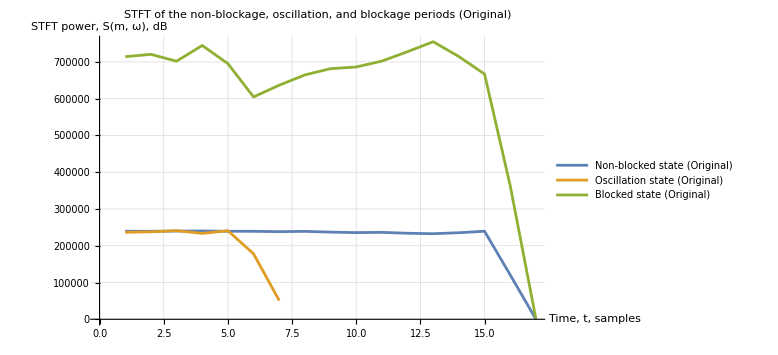
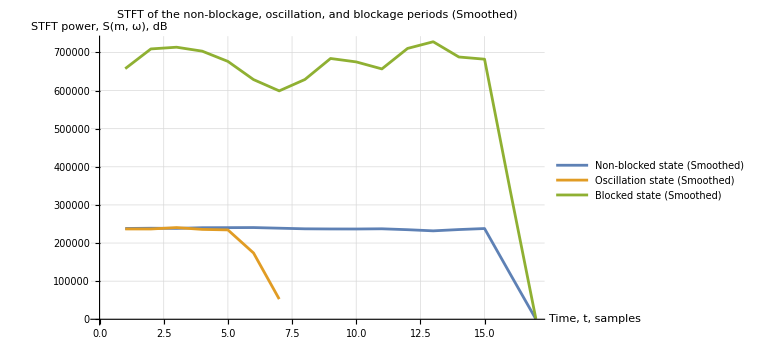
-Graphics-
-Graphics-
-Graphics-
-Graphics-